```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
```

# Taller 2 - Sistemas Dinámicos 2017-1 UdeA // Juan Esteban Aristizábal Zuluaga

## P. I

3.1.1	 ẋ=1+r x +x^2

```mathematica
f1[x_,r_]:=1+r*x +x^2
```

Puntos críticos del sistema:

```mathematica
Solve[{f1[x,r]==0},x]
```

{{x→1/2 (-r-√(-4+r^2))},{x→1/2 (-r+√(-4+r^2))}}

Los valores importantes a analizar son r =2    r < 2    y   r > 2.

Para r < 2 el sistema no tiene puntos fijos:
Campo vectorial para el S.D. con r<2

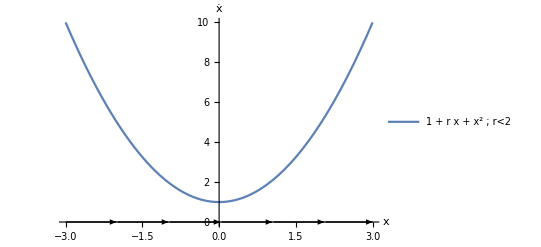

```mathematica
a11=
Plot[
f1[x,0],{x,-3,3},
AxesLabel->{"x","ẋ"},
PlotLegends->{"1 + r x + x^2 ; r<2 "},
Ticks->None
];

b11=
StreamPlot[
{f1[x,0],0},{x,-3,3},{y,-1,1},
StreamPoints->{{{{0,0},Black}}},
StreamScale->Large,
Frame->False
];

Show[a11,b11]
```

Para r = 2 el sistema tiene un punto fijo:

```mathematica
Solve[{f1[x,2]==0},x]
```

{{x→-1},{x→-1}}

```mathematica
D[f[x,2],x]/.x->-1
```

f^(1,0)[-1,2]

El análisis de estabilidad lineal no predice de qué tipo es este punto fijo, ya que   f 1 (-1)=0

En la gráfica de x vs. ẋ  se  puede ver que el único punto fijo del sistema x^*=-1 es semi-estable

Ahora se muestra el campo vectorial para el S.D. y r=2

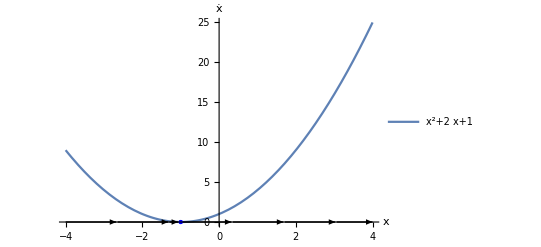

```mathematica
a12=
Plot[
f1[x,2],{x,-4,4},
AxesLabel->{"x","ẋ"},
PlotLegends->{{f1[x,2]}},
Ticks->Automatic
];

b12=
StreamPlot[
{f1[x,2],0},{x,-4,4},{y,1,-1},
StreamPoints->{{{{1,0},Black},{{-2,0},Black}}},
StreamScale->Large
];

c12=
ListPlot[
{{-1,0}},
PlotStyle->{Blue,PointSize[Large]}
];

Show[a12,b12,c12]
```

Por último, para r > 2 el sistema tiene dos puntos fijos  (se infiere de la forma general de las soluciones dadas al comienzo):

```mathematica
Solve[{f1[x,r]==0},x]
```

{{x→1/2 (-r-√(-4+r^2))},{x→1/2 (-r+√(-4+r^2))}}

```mathematica
D[f1[x,r],x]/.x->{1/2 (-r-√(-4+r^2)),1/2 (-r+√(-4+r^2))}
```

{-√(-4+r^2),√(-4+r^2)}

Por medio del análisis de estabilidad lineal, se puede ver en la operación anterior que uno de los puntos fijos (x^*=1/2 (-r-√(-4+r^2))) es estable y el otro (x^*=1/2 (-r+√(-4+r^2))) es inestable.

```mathematica
Solve[{f1[x,8^0.5]==0},x]
```

{{x→-2.41421},{x→-0.414214}}

Campo vectorial del S.D. para r>2

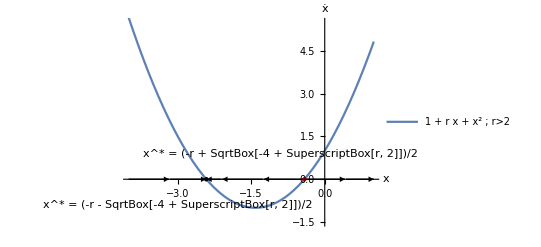

```mathematica
a13=
Plot[
f1[x,8^0.5],{x,-4,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{"1 + r x + x^2 ; r>2 "},
Ticks->None,
Epilog->{Text[Style["x^* = (-r - SqrtBox[-4 + SuperscriptBox[r, 2]])/2",Medium],{-3.0,-0.9}],
Text[Style["x^* = (-r + SqrtBox[-4 + SuperscriptBox[r, 2]])/2",Medium],{-0.90,.9}]}
];

b13=
StreamPlot[
{f1[x,8^0.5],0},{x,-4,1},{y,1,-1},
StreamPoints->{{{{1,0},Black},{{-2,0},Black},{{-3,0},Black}}},
StreamScale->Large,
Frame->False
];

c13=
ListPlot[
{{-2.41421,0}},
PlotStyle->{Black,PointSize[Large]},
Ticks->None
];

d13=
ListPlot[
{{-0.41421,0}},
PlotStyle->{Red,PointSize[Large]},
Ticks->None
];

Show[a13,b13,c13,d13,PlotRange-> {{-4,1},{-1.5,5.5}}]
```

Por último, el diagrama de bifurcación. La rama inestable en rojo y la rama estable en negro:

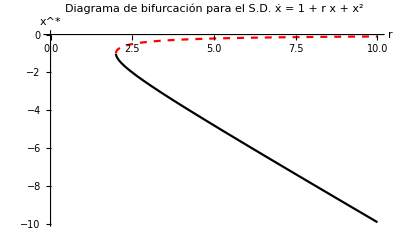

```mathematica
Plot[
{(-r-√(-4+r^2))/2,(-r+√(-4+r^2))/2},{r,0,10},
PlotStyle->{{Black},{Red,Dashed}},
PlotLabel->"Diagrama de bifurcación para el S.D. ẋ = 1 + r x + x^2",
AxesLabel->{"r","x^*"}
]
```

3.1.5	 
a)        ẋ=r^2 - x^2

```mathematica
f21[x_,r_]:=r^2 - x^2
```

Puntos críticos:

```mathematica
Solve[{f21[x,r]==0},x]
```

{{x→-r},{x→r}}

Para r<0:

Análisis de estabilidad lineal:

```mathematica
D[f21[x,r],x]/.x->{-r,r}
```

{2 r,-2 r}

Y como r<0 se infiere que x^*=-r  es estable y  x^*= r es inestable

Campo vectorial para r<0

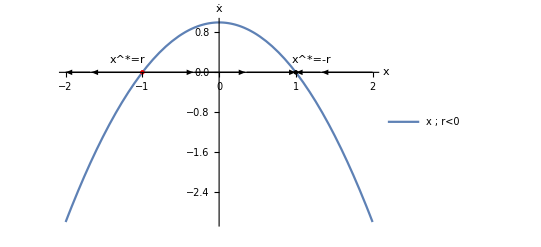

```mathematica
a21=
Plot[
f21[x,-1],{x,-2,2},
AxesLabel->{"x","ẋ"},
PlotLegends->{{"x ; r<0"}},
Epilog->{Text[Style["x^*=-r",Medium],{1.2,0.25}],
Text[Style["x^*=r",Medium],{-1.2,0.25}]},
Ticks->None
];

b21=
StreamPlot[
{f21[x,-1],0},{x,-2,2},{y,-1,1},
StreamPoints->{{{{-1.5,0},Black},{{1.5,0},Black},{{-0.5,0},Black},{{0.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c21=
ListPlot[
{{-1,0}},
PlotStyle->{Red,PointSize[Large]},
Ticks->None
];

d21=
ListPlot[
{{1,0}},
PlotStyle->{Black,PointSize[Large]},
Ticks->None
];

Show[a21,b21,c21,d21]
```

Para r>0:

Análisis de estabilidad lineal:

```mathematica
D[f21[x,r],x]/.x->{-r,r}
```

{2 r,-2 r}

Y como r>0, se infiere que x^*=-r  es inestable y  x^*= r es estable

Campo vectorial para r>0 :

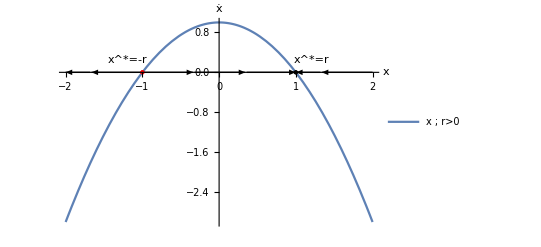

```mathematica
a22=
Plot[
f21[x,1],{x,-2,2},
AxesLabel->{"x","ẋ"},
PlotLegends->{{"x ; r>0"}},
Epilog->{Text[Style["x^*=r",Medium],{1.2,0.25}],
Text[Style["x^*=-r",Medium],{-1.2,0.25}]},
Ticks->None
];

Show[a22,b21,c21,d21]
```

Para r=0:

Análisis de estabilidad lineal:

```mathematica
Solve[f21[x,0]==0,x]
```

{{x→0},{x→0}}

```mathematica
D[f21[x,0],x]/.x->0
```

0

El criterio de estabilidad lineal no es concluyente. Por el método gráfico se infiere que el punto fijo x^*=0  es semi-estable

Campo vectorial para r = 0

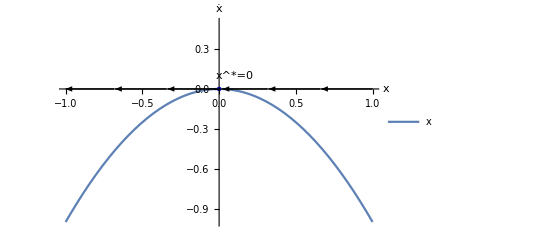

```mathematica
a25=
Plot[
f21[x,0],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{{"x"}},
Epilog->{Text[Style["x^*=0",Medium],{0.1,0.1}]},
Ticks->None,
PlotRange->{-1,0.5}
];

b25=
StreamPlot[
{f21[x,0],0},{x,-1,1},{y,-1,1},
StreamPoints->{{{{-.5,0},Black},{{.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c25=
ListPlot[
{{0,0}},
PlotStyle->{Blue,PointSize[Large]},
Ticks->None
];

Show[a25,b25,c25]
```

Ahora el diagrama de bifurcación:

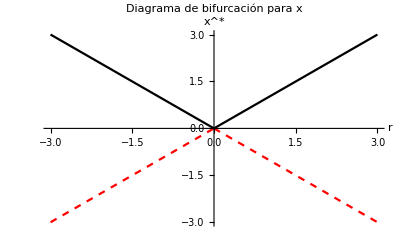

```mathematica
a23=
Plot[
{-r,r},{r,-3,0},
PlotStyle->{{Black},{Red,Dashed}},
AxesLabel->{"r","x^*"},
Ticks->None,
PlotLabel->"Diagrama de bifurcación para x"
];

a24=
Plot[
{r,-r},{r,0,3},
PlotStyle->{{Black},{Red,Dashed}},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para x",
Ticks->None
];

Show[a23,a24,PlotRange->{-3,3}]
```

b)        ẋ=r^2 + x^2

```mathematica
f22[x_,r_]:=r^2 + x^2
```

Puntos fijos del sistema:

```mathematica
Solve[{f22[x,r]==0},x]
```

{{x→-ⅈ r},{x→ⅈ r}}

La única forma de que la solución anterior pertenezca a los números reales (con r ∈ ℝ) es que r=0, en cuyo caso x^(*.1d)=0. De manera que solo hay dos formas principales del campo vectorial:

Para r=0:

Campo vectorial para el S.D. con r = 0

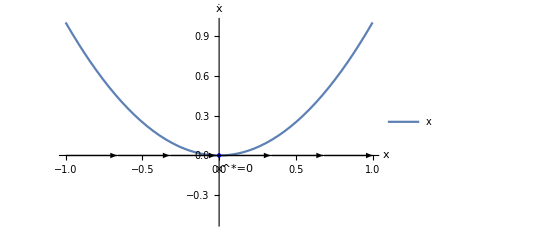

```mathematica
a26=
Plot[
f22[x,0],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{{"x"}},
Epilog->{Text[Style["x^*=0",Medium],{0.1,-0.1}]},
Ticks->None,
PlotRange->{-0.5,1}
];

b26=
StreamPlot[
{f22[x,0],0},{x,-1,1},{y,-1,1},
StreamPoints->{{{{-.5,0},Black},{{.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c26=
ListPlot[
{{0,0}},
PlotStyle->{Blue,PointSize[Large]},
Ticks->None
];

Show[a26,b26,c26]
```

Para r≠0:

```mathematica
Solve[{f22[x,r]==0},x]
```

{{x→-ⅈ r},{x→ⅈ r}}

Y como r≠0 , el sistema no tiene puntos fijos.

El campo vectorial queda:

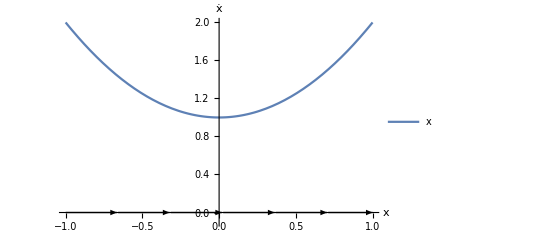

```mathematica
a27=
Plot[
f22[x,1],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{{"x"}},
Ticks->None,
PlotRange->{-0.1,2}
];

b27=
StreamPlot[
{f22[x,1],0},{x,-1,1},{y,-1,1},
StreamPoints->{{{{0,0},Black}}},
StreamScale->Large,
Frame->False
];

Show[a27,b27]
```

Así, el diagrama de bifurcación está compuesto únicamente por un punto (en realidad no hay bifurcación).

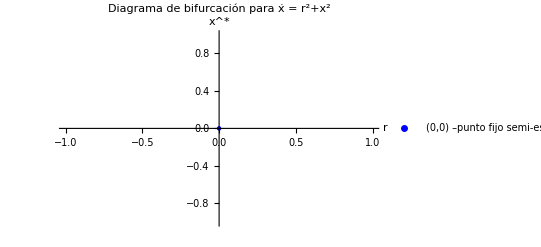

```mathematica
ListPlot[
{{0,0}},
PlotStyle->{Blue,PointSize[Large]},
AxesLabel->{"r","x^*"},
PlotLegends->{{"(0,0) –punto fijo\nsemi-estable"}},
PlotLabel->"Diagrama de bifurcación para ẋ = r^2+x^2",
Ticks->None
]
```

## P. II

3.2.4	  ẋ=x(r-ⅇ^x)

```mathematica
f3[x_,r_]:=x(r-ⅇ^x)
```

Puntos fijos:

```mathematica
pf3=Solve[{f3[x,r]==0,x∈Reals},x]
```

{{x→0},{x→ConditionalExpression[Log[r],r>0]}}

Análisis de estabilidad lineal:

```mathematica
est3=D[f3[x,r],x]/.x-> {0,ConditionalExpression[Log[r],r>0]}
```

{-1+r,ConditionalExpression[-r Log[r],r>0]}

De lo anterior se puede ver que existen “dos” bifurcaciones. En r_c=0  (de izquierda a derecha, se pasa de un punto fijo a dos puntos fijos)   y     r_c=1 (se cambia la estabilidad de los puntos fijos). Se analizarán los cuatro casos principales de los campos vectoriales:

Para r≤0 :

Solo existe un punto fijo (x^*=0) y es estable según criterio de estabilidad lineal.

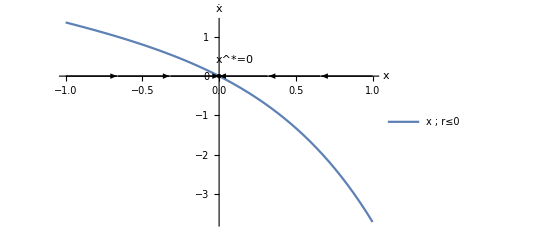

```mathematica
a31=
Plot[
f3[x,-1],{x,-1,1},
PlotLegends->{"x ; r≤0"},
AxesLabel->{"x","ẋ"},
Ticks->None,
Epilog->{Text[Style["x^*=0",Medium],{0.1,0.4}]}
];

b31=
StreamPlot[
{f3[x,-1],0},{x,-1,1},{y,-1,1},
StreamPoints->{{{{-0.5,0},Black},{{0.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c31=
ListPlot[
{{0,0}},
PlotStyle->{Black, PointSize[Large]},
Ticks->None
];

Show[a31,b31,c31]
```

Para 0<r<1 :

Puntos fijos:

```mathematica
pf3
```

{{x→0},{x→ConditionalExpression[Log[r],r>0]}}

Análisis de estabilidad lineal:

```mathematica
est3
```

{-1+r,ConditionalExpression[-r Log[r],r>0]}

Existen dos puntos fijos: x^*=0 que es estable   ;   x^*=Log(r) , el cual es inestable (ambos según criterio de estabilidad lineal).


Campo vectorial para el S.D. con 0<r<1

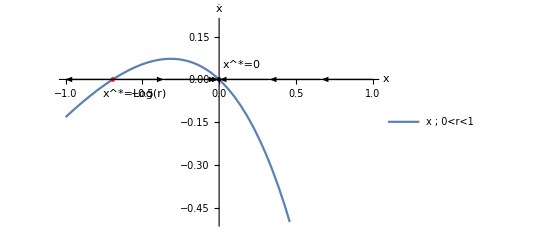

```mathematica
a32=
Plot[
f3[x,0.5],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{"x ; 0<r<1"},
PlotRange->{-0.5,0.2},
Epilog->{Text[Style["x^*=0",Medium],{0.15,0.05}],
Text[Style["x^*=Log(r)",Medium],{-0.55,-0.05}]},
Ticks->None
];

b32=
StreamPlot[
{f3[x,0.5],0},{x,-1,1},{y,-0.5,0.2},
StreamPoints->{{{{-0.8,0},Black},{{0.8,0},Black},{{-0.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c32=
ListPlot[
{{0,0}},
PlotStyle->{Black,PointSize[Large]},
Ticks->None
];

d32=
ListPlot[
{{Log[0.5],0}},
PlotStyle->{Red,PointSize[Large]},
Ticks->None
];

Show[a32,b32,c32,d32]
```

Para r=1 :

Punto fijo:

```mathematica
pf3/.r->1
```

{{x→0},{x→0}}

Análisis de estabilidad lineal:

```mathematica
est3/.r->1
```

{0,0}

El criterio de estabilidad lineal no es concluyente.

Por el método gráfico se puede ver que el único punto fijo para este caso es semi-estable.

Campo vectorial para el S.D. con r=1

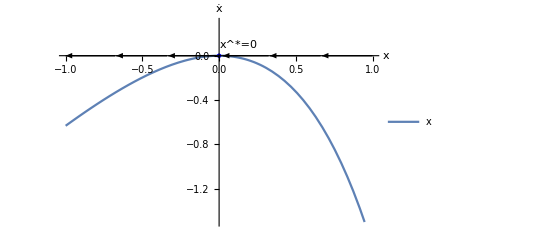

```mathematica
a33=
Plot[
f3[x,1],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{"x"},
Epilog->{Text[Style["x^*=0",Medium],{0.13,0.1}]},
PlotRange->{-1.5,0.3},Ticks->None
];

b33=
StreamPlot[
{f3[x,1],0},{x,-1,1},{y,-0.5,0.2},
StreamPoints->{{{{-0.5,0},Black},{{0.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c33=
ListPlot[
{{0,0}},
PlotStyle->{Blue,PointSize[Large]},
Ticks->None
];

Show[a33,b33,c33]
```

Por último, para r>1 :

Puntos fijos:

```mathematica
pf3
```

{{x→0},{x→ConditionalExpression[Log[r],r>0]}}

Análisis de estabilidad lineal:

```mathematica
est3
```

{-1+r,ConditionalExpression[-r Log[r],r>0]}

Se nota que teniendo en cuenta que r>1,  x^*=0 pasa a ser inestable y x^*=Log(r) pasa a ser estable.

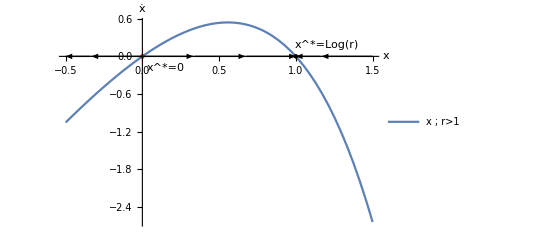

```mathematica
a34=
Plot[
f3[x,ⅇ],{x,-0.5,1.5},
AxesLabel->{"x","ẋ"},
PlotLegends->{"x ; r>1"},
Epilog->{Text[Style["x^*=0",Medium],{0.15,-0.18}],
Text[Style["x^*=Log(r)",Medium],{1.2,0.18}]},
Ticks->None
];

b34=
StreamPlot[
{f3[x,ⅇ],0},{x,-0.5,1.5},{y,-0.5,0.2},
StreamPoints->{{{{-0.3,0},Black},{{0.3,0},Black},{{1.2,0},Black}}},
StreamScale->Large,
Frame->False
];

c34=
ListPlot[
{{1,0}},
PlotStyle->{Black,PointSize[Large]},
Ticks->None
];

d34=
ListPlot[
{{0,0}},
PlotStyle->{Red,PointSize[Large]},
Ticks->None
];

Show[a34,b34,c34,d34]
```

Ahora el diagrama de bifurcación:

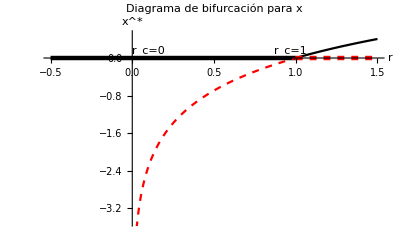

```mathematica
a35=
Plot[
0,{r,-0.5,1},
PlotStyle->{Black,Thickness[0.008]},
PlotLabel->"Diagrama de bifurcación para x",
AxesLabel->{"r","x^*"},
Ticks->None,
Axes->{True,True}
];

a36=
Plot[
Log[r],{r,0,1},
PlotStyle->{Red,Dashed},
PlotLabel->"Diagrama de bifurcación para x",
AxesLabel->{"r","x^*"},
Ticks->None,
Axes->{True,True}
];

a37=
Plot[
{Log[r],0},{r,1,1.5},
PlotStyle->{{Black},{Red,Dashed,Thickness[0.008]}},
PlotLabel->"Diagrama de bifurcación para x",
AxesLabel->{"r","x^*"},
Ticks->None,
Axes->{True,True}
];

Show[
a35,a36,a37,
PlotRange->{-3.5,.5},
Epilog->{Text[Style["r_c=0"],{0.1,0.15}],
Text[Style["r_c=1"],{0.97,0.15}]}
]
```

3.4.3	  ẋ=x(r-4 x^2)

```mathematica
f4[x_,r_]:=x(r-4 x^2)
```

Puntos fijos:

```mathematica
pf4=Solve[f4[x,r]==0,x]
```

{{x→0},{x→-(√r)/2},{x→(√r)/2}}

Análisis de estabilidad lineal

```mathematica
est4=D[f4[x,r],x]/.x->{0,-(√r)/2,(√r)/2}
```

{r,-2 r,-2 r}

En este caso la bifurcación se da en r_c=0, ya que en ese punto se cumplen las dos condiciones:  r=4 x^2   y    ⅆ/ⅆx(r)=4ⅆ/ⅆx(x^2)
Existen entonces tres casos principales para el campo vectorial:

Para r<0:

Puntos fijos:

```mathematica
pf4/.r->ConditionalExpression[r,r<0&&r∈Reals]
```

{{x→0},{x→ConditionalExpression[-(√r)/2,r∈Reals&&r<0]},{x→ConditionalExpression[(√r)/2,r∈Reals&&r<0]}}

Existe solo 1 punto fijo

Análisis de estabilidad lineal:

```mathematica
est4
```

{r,-2 r,-2 r}

Como r<0  se infiere que el único punto fijo x^*= 0 es estable.

Campo vectorial para el S.D. con r<0

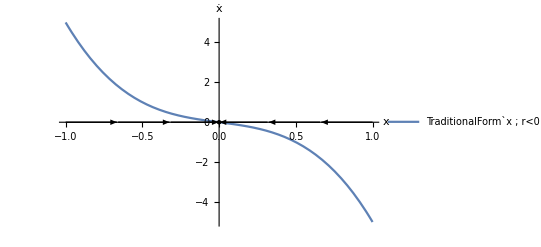

```mathematica
a41=
Plot[
f4[x,-1],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{"TraditionalForm`x  ;  r<0"},
Ticks->None
];

b41=
StreamPlot[
{f4[x,-1],0},{x,-1,1},{y,-1,1},
StreamPoints->{{{{-0.5,0},Black},{{0.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c41=
ListPlot[
{{0,0}},
PlotStyle->{Black,PointSize[Large]},
Ticks->None
];

Show[a41,b41,c41]
```

Para r=0:

Puntos fijos:

```mathematica
pf4/.r->0
```

{{x→0},{x→0},{x→0}}

Existe solo 1 punto fijo

Análisis de estabilidad lineal:

```mathematica
est4/.r->0
```

{0,0,0}

El criterio de análisis de estabilidad lineal no es concluyente. Mediante el método gráfico se puede ver que el único punto fijo, x^*=0, es estable: 

Campo vectorial para el S.D. con r=0

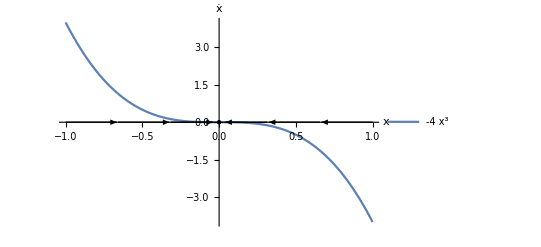

```mathematica
a42=
Plot[
f4[x,0],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{{f4[x,0]}},
Ticks->None
];

b42=
StreamPlot[
{f4[x,0],0},{x,-1,1},{y,-1,1},
StreamPoints->{{{{-0.5,0},Black},{{0.5,0},Black}}},
StreamScale->Large,
Frame->False
];

c42=
ListPlot[
{{0,0}},
PlotStyle->{Black,PointSize[Large]},
Ticks->None
];

Show[a42,b42,c42]
```

Por último, para r>0:

Puntos fijos:

```mathematica
pf4
```

{{x→0},{x→-(√r)/2},{x→(√r)/2}}

Existen tres puntos fijos.

Análisis de estabilidad lineal:

```mathematica
est4
```

{r,-2 r,-2 r}

Teniendo en cuenta que r>0 y por el criterio de análisis de estabilidad lineal,  x^*=0 es inestable mientras que  x^*=±(√r)/2  son inestables 

Campo vectorial para el S.D. con r>0

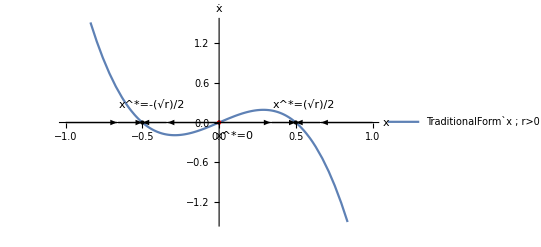

```mathematica
a43=
Plot[
f4[x,1],{x,-1,1},
AxesLabel->{"x","ẋ"},
PlotLegends->{"TraditionalForm`x  ;  r>0"},
Ticks->None,
Epilog->{Text[Style["x^*=0",Medium],{0.1,-0.2}],
Text[Style["x^*=-(√r)/2",Medium],{-0.44,0.28}],
Text[Style["x^*=(√r)/2",Medium],{0.55,0.28}]}
];

b43=
StreamPlot[
{f4[x,1],0},{x,-1,1},{y,-1,1},
StreamPoints->{{{{-0.25,0},Black},{{0.25,0},Black},{{-0.75,0},Black},{{0.75,0},Black}}},
StreamScale->Large,Frame->False
];

c43=
ListPlot[
{{0,0}},
PlotStyle->{Red,PointSize[Large]},
Ticks->None
];

d43=
ListPlot[
{{0.5,0},{-0.5,0}},
PlotStyle->{Black,PointSize[Large]},
Ticks->None
];

Show[a43,b43,c43,d43]
```

Ahora el diagrama de bifurcación:

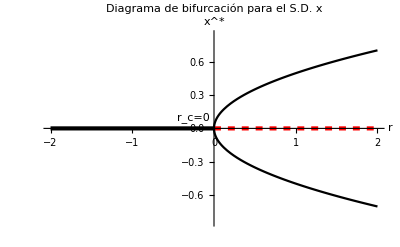

```mathematica
a44=
Plot[
0,{r,-2,0},
PlotStyle->{Black,Thickness[0.0075]},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
Ticks->None
];

a45=
Plot[
{{0},{-(√r)/2},{(√r)/2}},{r,0,2},
PlotStyle->{{Red,Dashed,Thickness[0.0075]},{Black},{Black}},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
Ticks->None
];

Show[
a44,a45,
Epilog->{Text[Style["r_c=0",Medium],{-0.25,0.1}]},
PlotRange->{-1.7/2,1.7/2}
]
```

Es claro que la bifurcación de tridente de este sistema dinámico es súper-crítica.

## P. III

3.4.7	 ẋ=5-r ⅇ^(-x^2)

```mathematica
f5[x_,r_]:=5-r ⅇ^(-x^2)
```

Puntos fijos:

```mathematica
pf5=Solve[{f5[x,r]==0,x∈Reals},x]
```

{{x→ConditionalExpression[-√Log[r/5],r≥5]},{x→ConditionalExpression[√Log[r/5],r≥5]}}

Análisis de estabilidad lineal:

```mathematica
est5=D[f5[x,r],x]/.x->{ConditionalExpression[-√Log[r/5],r≥5],ConditionalExpression[√Log[r/5],r≥5]}
```

{ConditionalExpression[-10 √Log[r/5],r≥5],ConditionalExpression[10 √Log[r/5],r≥5]}

Es claro que el punto en el que ocurre la bifurcación es en r_c=5. Para valores de  r<r_c  no existen puntos fijos. Para valores de  r>r_c aparecen dos ramas: una estable y otra inestable. Se deduce que la bifurcación es del tipo “punto de silla”.
Es claro que el punto fijo x^*=-√Log[r/5]  es estable y   x^*=√Log[r/5] es inestable.

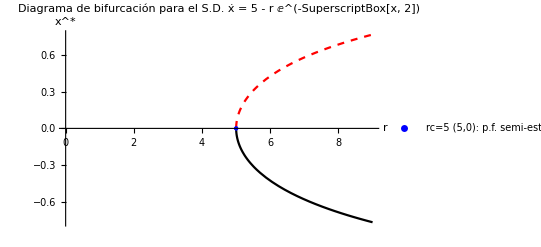

```mathematica
a51=
Plot[
{-√Log[r/5],√Log[r/5]},{r,0,9},
PlotStyle->{{Black},{Red,Dashed}},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. ẋ = 5 - r ⅇ^(-SuperscriptBox[x, 2])"
];

a52=
ListPlot[
{{5,0}},
PlotStyle->{Blue,PointSize[Large]},
PlotLegends->{"rc=5\n(5,0): p.f. semi-estable.\nBif. punto de Sill.a"}
];
Show[a51,a52]
```

3.4.10	 ẋ=x*(r+x^2/(1+x^2))

```mathematica
f6[x_,r_]:=x*(r+x^2/(1+x^2))
```

Puntos Fijos:

```mathematica
pf6=Solve[{f6[x,r]==0,r∈Reals,x∈Reals},x]
```

{{x→ConditionalExpression[0,-1<r<0||r>0||r<-1]},{x→ConditionalExpression[-√(-r/(1+r)),-1<r<0]},{x→ConditionalExpression[√(-r/(1+r)),-1<r<0]}}

Análisis de estabilidad lineal:

```mathematica
est6=Simplify[D[f6[x,r],x]/.x->{0,ConditionalExpression[-√(-r/(1+r)),-1<r<0],ConditionalExpression[√(-r/(1+r)),-1<r<0]}]
```

{r,ConditionalExpression[-2 r (1+r),-1<r<0],ConditionalExpression[-2 r (1+r),-1<r<0]}

```mathematica
{r,ConditionalExpression[-2 r (1+r),-1<r<0],ConditionalExpression[-2 r (1+r),-1<r<0]}
```

{r,ConditionalExpression[-2 r (1+r),-1<r<0],ConditionalExpression[-2 r (1+r),-1<r<0]}

```mathematica
rc6=Solve[{D[f6[x,r],x]==0,f6[x,r]==0},{x,r}]
```

{{x→0,r→0}}

En este caso aparecen dos puntos críticos en la bifurcación: r_c=-1  y  r_c=0. Existen 3 casos diferentes de campos vectoriales:

a)  r≤-1  :  Existe un único punto fijo   x^*=0  el cual es estable, según análisis de estabilidad lineal.
b)  -1<r<0  :  Existen tres puntos fijos x^*=0 , el cual es estable y x^*=±√(-r/(1+r)) los cuales son inestables (análisis de estabilidad lineal).
c)  r=0  :  Existe un único punto fijo x*=0 , el cual es inestable (análisis gráfico).
d)  r>0  :  Existe un único punto fijo, el cual es inestable (análisis de estabilidad lineal)

Los casos anteriores se pueden ver manipulando la siguiente gráfica.

```mathematica
Manipulate[
Plot[
f6[x,r],{x,-10,10},
AxesLabel->{"x","ẋ"},
PlotLegends->{{f6[x,r]}}
],
{r,-2,0.5}
]
```

El diagrama de bifurcación queda así:

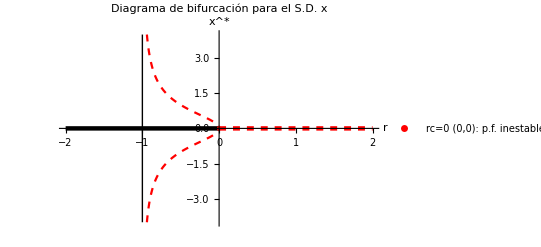

```mathematica
a61=
Plot[
{0,-√(-r/(1+r)),√(-r/(1+r))},{r,-2,0},
Exclusions->{1+r==0},
PlotRange->{-4,4},
PlotStyle->{{Black,Thickness[0.008]},{Red,Dashed},{Red,Dashed}},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x"
];

a62=
Plot[
0,{r,0,2},
PlotStyle->{Red,Dashed,Thickness[0.008]},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x"
];

a63=
ListPlot[
{{0,0}},
PlotStyle->{Red,PointSize[Large]},
PlotLegends->{"rc=0\n(0,0): p.f. inestable.\nBif. tridente sub-crítica."}
];

Show[
a61,a62,a63,
PlotRange->{{-2,2},{-4,4}},
Epilog->{Style[Line[{{-1,-4},{-1,4}}],Dashed]}
]
```

· Es claro que la bifurcación en r_c=0 es una forma especial del tipo tridente sub-crítica, ya que las tres ramificaciones no se mantienen para r<0, sino solo para -1<r<0. 

· Para r≤-1 se mantiene únicamente la rama estable (x^*=0   ∀ r<-1). 

· La línea negra a rayas  r=-1 denota únicamente el comportamiento asintótico de las dos ramas inestables que existen para  -1<r<0 y de ninguna manera muestra puntos fijos en el diagrama de bifurcación (i.e. para r=-1 solo existe un punto fijo :  x^*=0).

## P. IV

3.6.3	 ẋ=x(r+a x+x^2)       

NOTAS: 

·Me equivoqué en uno de los signos del ejercicio original –era    ẋ=x(r+a x-x^2)     en vez de    ẋ=x(r+a x+x^2)–  lo que resultó en que mi análisis es a perturbaciónes de la bifurcación tridente sub-crítica y NO de la super-crítica. 

·No lo corrijo porque apenas me doy cuenta antes de montarlo a la plataforma (ya no me da tiempo de corregirlo) y serían muchos detalles los que habría que cambiar (“labels” de gráficas “dashing’s” de líneas, colores de líneas, etc.). Sin embargo, el análisis del ejercicio tal y como lo planteo está bien hecho.

```mathematica
f7[x_,r_,a_]:=x*(r+a*x+x^2)
```

Puntos fijos del sistema:3

```mathematica
{pf71,pf72,pf73}=x/.Solve[f7[x,r,a]==0,x]
```

{0,1/2 (-a-√(a^2-4 r)),1/2 (-a+√(a^2-4 r))}

Análisis de estabilidad lineal:

```mathematica
est7=Simplify[D[f7[x,r,a],x]/.x->{0,1/2 (-a-√(a^2-4 r)),1/2 (-a+√(a^2-4 r))}]
```

{r,1/2 (a^2+a √(a^2-4 r)-4 r),1/2 (a^2-a √(a^2-4 r)-4 r)}

Superficie que muestra los puntos fijos del sistema según sean los parámetros a y r

```mathematica
Plot3D[
{0,1/2 (-a-√(a^2-4 r)),1/2 (-a+√(a^2-4 r))},{r,-4,4},{a,-4,4},
AxesLabel->{"r","a","x^*"},
PlotStyle->{{RGBColor[0.368417,0.506779,0.709798]},{RGBColor[0.368417,0.506779,0.709798]},{RGBColor[0.368417,0.506779,0.709798]}},
AspectRatio->0.7
]
```

-Graphics3D-

Puntos críticos para los parámetros, en el plano de la curva de bifurcación (a_c ,r_c ):

```mathematica
rc7={a,r}/.Solve[{f7[x,r,a]==0,D[f7[x,r,a],x]==0},{a,r}][[1]]
```

{-2 x,x^2}

Los diagramas de bifurcación x^*vs. r cualitativamente diferentes se dan cuando:
·  a<0  
	La rama x^*=0 es estable mientras r < 0 y es inestable mientras r>0.
	La rama x^*=1/2 (-a-√(a^2-4 r)) es estable mientras 0<r<a^2/4  y es inestable para r<0..
	La rama x^*=1/2 (-a+√(a^2-4 r)) es inestable.
·  a=0  
	La rama x^*=0 es estable mientras r < 0 y es inestable mientras r>0.
	La rama x^*=-1/2 √(-4 r) es inestable.
	La rama x^*=1/2 √(-4 r) es inestable.	
·  a>0  
	La rama x^*=0 es estable mientras r < 0 y es inestable mientras r>0.
	La rama x^*=1/2 (-a-√(a^2-4 r)) es inestable.
	La rama x^*=1/2 (-a+√(a^2-4 r)) es estable mientras 0<r<a^2/4  y es inestable para r<0.

```mathematica
f71[r_,a_]:=1/2 (-a-√(a^2-4 r))
f72[r_,a_]:=1/2 (-a+√(a^2-4 r))
```

```mathematica
Reduce[{a^2+a √(a^2-4 r)-4 r<0,a<0},r,Reals]
Reduce[{a^2+a √(a^2-4 r)-4 r>0,a<0},r,Reals]
Reduce[{a^2-a √(a^2-4 r)-4 r<0,a<0},r,Reals]
Reduce[{a^2-a √(a^2-4 r)-4 r>0,a<0},r,Reals]
```

a<0&&0<r<a^2/4

a<0&&r<0

False

a<0&&r<a^2/4

```mathematica
Reduce[{a^2+a √(a^2-4 r)-4 r<0,a==0},r,Reals]
Reduce[{a^2+a √(a^2-4 r)-4 r>0,a==0},r,Reals]
Reduce[{a^2-a √(a^2-4 r)-4 r<0,a==0},r,Reals]
Reduce[{a^2-a √(a^2-4 r)-4 r>0,a==0},r,Reals]
```

False

a==0&&r<0

False

a==0&&r<0

```mathematica
Reduce[{a^2+a √(a^2-4 r)-4 r<0,a>0},r,Reals]
Reduce[{a^2+a √(a^2-4 r)-4 r>0,a>0},r,Reals]
Reduce[{a^2-a √(a^2-4 r)-4 r<0,a>0},r,Reals]
Reduce[{a^2-a √(a^2-4 r)-4 r>0,a>0},r,Reals]
```

False

a>0&&r<a^2/4

a>0&&0<r<a^2/4

a>0&&r<0

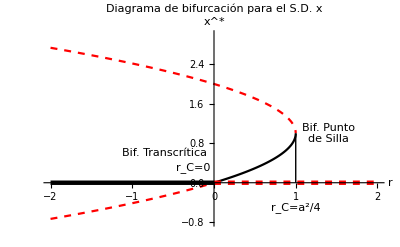

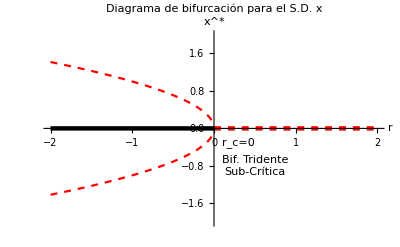

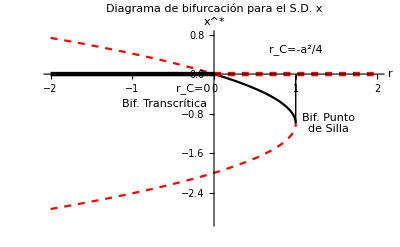

```mathematica
a71=
Plot[
{f71[r,-2],0},{r,-2,0},
PlotStyle->{{Red,Dashed},{Black,Thickness[0.008]}},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",Ticks->None
];

a72=
Plot[
f71[r,-2],{r,0,1},
PlotStyle->{Black},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
Ticks->None
];

a73=
Plot[
f72[r,-2],{r,-2,2},
PlotStyle->{Red,Dashed},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
Ticks->None
];

a74=
Plot[
0,{r,0,2},
PlotStyle->{Red,Dashed,Thickness[0.008]},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
Ticks->None
];

Show[a71,a72,a73,a74,
PlotRange->{{-2,2},{-0.8,3}},
Epilog->{Style[Line[{{1,0},{1,1}}],Dashed],
Text[Style["r_C=a^2/4",Medium],{1,-0.5}],
Text[Style["r_C=0",Medium],{-0.25,0.3}],
Text[Style["Bif. Transcrítica",Medium],{-.6,0.6}],
Text[Style["Bif. Punto\nde Silla",Medium],{1.4,1}]}
]

a75=
Plot[
{f71[r,0],f72[r,0],0},{r,-2,0},
PlotStyle->{{Red,Dashed},{Red,Dashed},{Black,Thickness[0.008]}},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x"
];

a76=
Plot[
0,{r,0,2},
PlotStyle->{Red,Dashed,Thickness[0.008]},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x"
];

Show[
a75,a76,
PlotRange->{{-2,2},{-2,2}},
Epilog->{Text[Style["r_c=0",Medium],{0.3,-0.3}],
Text[Style["Bif. Tridente\nSub-Crítica",Medium],{.5,-0.8}]}
]

a77=
Plot[
f71[r,2],{r,-2,2},
PlotStyle->{Red,Dashed},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
AxesOrigin->{0,0},
Ticks->None
];

a78=
Plot[
f72[r,2],{r,0,1},
PlotStyle->{Black},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
AxesOrigin->{0,0},
Ticks->None
];

a79=
Plot[
{f72[r,2],0},{r,-2,0},
PlotStyle->{{Red,Dashed},{Black,Thickness[0.008]}},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
AxesOrigin->{0,0},
Ticks->None
];

a710=
Plot[
0,{r,0,2},
PlotStyle->{Red,Dashed,Thickness[0.008]},
AxesLabel->{"r","x^*"},
PlotLabel->"Diagrama de bifurcación para el S.D. x",
AxesOrigin->{0,0},
Ticks->None
];

Show[
a77,a78,a79,a710,
PlotRange->{{-2,2},{-3,0.8}},
Epilog->{Style[Line[{{1,0},{1,-1}}],Dashed],
Text[Style["r_C=-a^2/4",Medium],{1,0.5}],
Text[Style["r_C=0",Medium],{-0.25,-0.3}],
Text[Style["Bif. Transcrítica",Medium],{-.6,-0.6}],
Text[Style["Bif. Punto\nde Silla",Medium],{1.4,-1}]}
]
```

b)

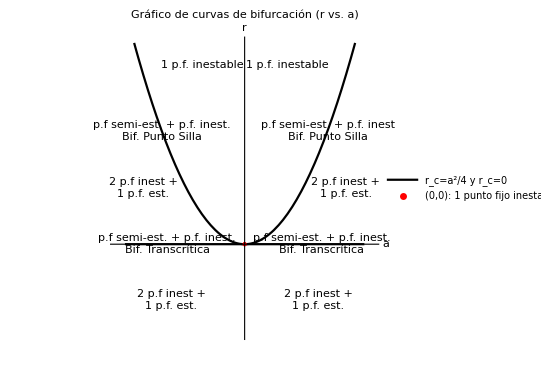

```mathematica
a711=
ParametricPlot[
{-2 x,x^2},{x,-3,3},
PlotRange->{{-7,7},{-4,9}},
PlotStyle->Black, 
PlotLabel->"Gráfico de curvas de bifurcación (r vs. a)",
AxesLabel->{"a","r"},
Epilog->{Rotate[Text[Style["p.f semi-est. + p.f. inest\nBif. Punto Silla",Medium],{4.5,(4.5^2)/4}],1.16],
Rotate[Text[Style["p.f semi-est. + p.f. inest.\nBif. Punto Silla",Medium],{-4.5,(4.5^2)/4}],-1.16],Text[Style["1 p.f. inestable",Medium],{-2.3,8}],
Text[Style["1 p.f. inestable",Medium],{2.3,8}],
Text[Style["p.f semi-est. + p.f. inest.\nBif. Transcrítica",Medium],{-4.2,0}],Text[Style["p.f semi-est. + p.f. inest.\nBif. Transcrítica",Medium],{4.2,0}],
Text[Style["2 p.f inest +\n1 p.f. est.",Medium],{-4,-2.5}],
Text[Style["2 p.f inest +\n1 p.f. est.",Medium],{4,-2.5}],
Text[Style["2 p.f inest +\n1 p.f. est.",Medium],{-5.5,2.5}],
Text[Style["2 p.f inest +\n1 p.f. est.",Medium],{5.5,2.5}]},
Ticks->None
];

a712=
Plot[
0,{x,-6.5,6.5},PlotStyle->{Black},
PlotLegends->{"r_c=a^2/4  y  r_c=0"},
Epilog->{Line[{{0,-3.9},{0,8.9}}]},
PlotLabel->"Gráfico de curvas de vifurcación (r vs. a)",
AxesLabel->{"a","r"},
Ticks->None
];

a713=
ListPlot[
{{0,0}},
PlotStyle->{Red,PointSize[Large]},
PlotLegends->{"(0,0): 1 punto fijo\ninestable –Bifurcación\nde Tridente sub-crírtica"}
];

Show[
a711,a712,a713,
PlotRange->{{-7,7},{-4,9}},
Ticks->None
]
```

·Las bifurcaciones mencionadas se dan en el plano (r,x^*) para un a fijo.

## P. V

3.7.1

El sistema dinámico en forma a-dimensional es ⅆx/ⅆτ=r x(1-x/k)-x^2/(1+x^2)

```mathematica
f81[x_,r_,k_]:=r*x*(1-x/k)-x^2/(1+x^2)
```

Es fácil ver que x=0 es siempre un punto fijo :

```mathematica
f81[x,r,k]/.x->0
```

0

Análisis de estabilidad lineal:

```mathematica
est8=D[f81[x,r,k],x]
```

-(r x)/k+r (1-x/k)+(2 x^3)/((1+x^2)^2)-(2 x)/(1+x^2)

```mathematica
est8/.x->0
```

r

el parámetro r está relacionado con los parámetros A, R , B  > 0 así: r=(R A)/B  de manera que el parámetro r siempre debe ser mayor que cero y por el criterio de análisis de estabilidad lineal, el punto fijo r=0 es siempre inestable.

3.7.2

a) Según las ecuaciones 3.7.8 y 3.7.9 r(x)  y k(x)  están dados por :

```mathematica
r1[x_]:=(2 x^3)/((1+x^2)^2)
k1[x_]:=(2 x^3)/(-1+x^2)
```

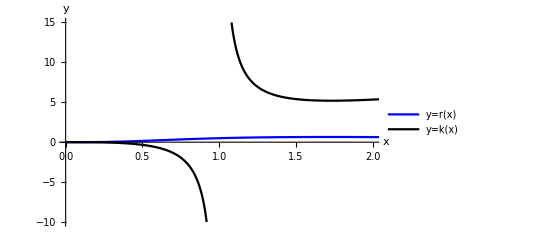

```mathematica
a81=
Plot[
{r1[x],k1[x]},
{x,0,3},
PlotStyle->{{Blue},{Black}},
AxesLabel->{"x","y"},
PlotLegends->{"y=r(x)","y=k(x)"},
PlotRange->{{0,2},{-10,15}}
]
```

```mathematica
Limit[r1[x],x-> 1]
Limit[k1[x],x->1]
Limit[r1[x],x->Infinity]
Limit[k1[x],x->Infinity]
```

1/2

∞

0

∞

Los límites calculados anteriormente indican que la curva de bifurcación debe tener una asíntota en r=0 y otra en r=1/2

b) El punto de cúspide de la figura 3.7.5 se da cuando ⅆr/ⅆk(x)=(ⅆr/ⅆx)/(ⅆk/ⅆx) tenga alguna indeterminación.

```mathematica
D[r1[x],x]/D[k1[x],x]
```

(-(8 x^4)/((1+x^2)^3)+(6 x^2)/((1+x^2)^2))/(-(4 x^4)/((-1+x^2)^2)+(6 x^2)/(-1+x^2))

En el numerador no existen indeterminaciones, por lo que se puede deducir que el pico de la gráfica se da cuando el denominador es igual a cero:  (4 x^4)/((-1+x^2)^2)=(6 x^2)/(-1+x^2)

```mathematica
Solve[-(4 x^4)/((-1+x^2)^2)+(6 x^2)/(-1+x^2)==0,x]
```

{{x→0},{x→0},{x→-√3},{x→√3}}

De la condición k>0 y de k(x) se deduce que x debe ser mayor que 1. Por tanto, el pico se da en x=√3. esto es, se da en:

```mathematica
{k1[√3],r1[√3]}
```

{3 √3,(3 √3)/8}

(r,k)=(3 √3,(3 √3)/8)

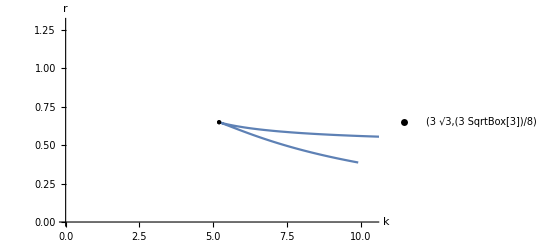

```mathematica
a82=
ParametricPlot[
{k1[x],r1[x]},{x,1.001,√3+3},
PlotRange->{{5,6},{0.5,0.7}},
AspectRatio->0.7
];
a83=
ListPlot[
{{3 √3,(3 √3)/8}},
PlotStyle->{Black,PointSize[Large]},
PlotLegends->{"(3 √3,(3 SqrtBox[3])/8)"}
];
Show[a83,a82,AxesLabel->{"k","r"},Axes->True]
```